```mathematica
Sigma[0] = SparseArray[IdentityMatrix[2]];
Sigma[1] = SparseArray[{{0, 1}, {1, 0}}];
Sigma[2] = SparseArray[{{0, -I}, {I, 0}}];
Sigma[3] = SparseArray[{{1, 0}, {0, -1}}];
```

```mathematica
H = 0.5KroneckerProduct[Sigma[0], Sigma[1]] + 0.5KroneckerProduct[Sigma[2], Sigma[3]]
```

SparseArray[…]

```mathematica
H = SparseArray[{
{1,1}->13.000+0.000 I,{1,8}->-0.500+0.000 I,{1,10}->0.000+0.000 I,{1,19}->0.000+0.000 I,{1,37}->0.000+0.000 I,{1,57}->-0.500+0.000 I,{2,2}->11.000+0.000 I,{2,7}->0.000+0.000 I,{2,9}->-2.000+0.000 I,{2,20}->0.000+0.000 I,{2,38}->0.000+0.000 I,{2,58}->-0.500+0.000 I,{3,3}->11.000+0.000 I,{3,6}->0.000+0.000 I,{3,12}->0.000+0.000 I,{3,17}->-2.000+0.000 I,{3,39}->0.000+0.000 I,{3,59}->-0.500+0.000 I,{4,4}->9.000+0.000 I,{4,5}->0.000+0.000 I,{4,11}->-2.000+0.000 I,{4,18}->-2.000+0.000 I,{4,40}->0.000+0.000 I,{4,60}->-0.500+0.000 I,{5,4}->0.000+0.000 I,{5,5}->11.000+0.000 I,{5,14}->0.000+0.000 I,{5,23}->0.000+0.000 I,{5,33}->-2.000+0.000 I,{5,61}->-0.500+0.000 I,{6,3}->0.000+0.000 I,{6,6}->9.000+0.000 I,{6,13}->-2.000+0.000 I,{6,24}->0.000+0.000 I,{6,34}->-2.000+0.000 I,{6,62}->-0.500+0.000 I,{7,2}->0.000+0.000 I,{7,7}->9.000+0.000 I,{7,16}->0.000+0.000 I,{7,21}->-2.000+0.000 I,{7,35}->-2.000+0.000 I,{7,63}->-0.500+0.000 I,{8,1}->-0.500+0.000 I,{8,8}->7.000+0.000 I,{8,15}->-2.000+0.000 I,{8,22}->-2.000+0.000 I,{8,36}->-2.000+0.000 I,{8,64}->-0.500+0.000 I,{9,2}->-2.000+0.000 I,{9,9}->11.000+0.000 I,{9,16}->-0.500+0.000 I,{9,27}->0.000+0.000 I,{9,45}->0.000+0.000 I,{9,49}->0.000+0.000 I,{10,1}->0.000+0.000 I,{10,10}->13.000+0.000 I,{10,15}->0.000+0.000 I,{10,28}->0.000+0.000 I,{10,46}->0.000+0.000 I,{10,50}->0.000+0.000 I,{11,4}->-2.000+0.000 I,{11,11}->9.000+0.000 I,{11,14}->0.000+0.000 I,{11,25}->-2.000+0.000 I,{11,47}->0.000+0.000 I,{11,51}->0.000+0.000 I,{12,3}->0.000+0.000 I,{12,12}->11.000+0.000 I,{12,13}->0.000+0.000 I,{12,26}->-2.000+0.000 I,{12,48}->0.000+0.000 I,{12,52}->0.000+0.000 I,{13,6}->-2.000+0.000 I,{13,12}->0.000+0.000 I,{13,13}->9.000+0.000 I,{13,31}->0.000+0.000 I,{13,41}->-2.000+0.000 I,{13,53}->0.000+0.000 I,{14,5}->0.000+0.000 I,{14,11}->0.000+0.000 I,{14,14}->11.000+0.000 I,{14,32}->0.000+0.000 I,{14,42}->-2.000+0.000 I,{14,54}->0.000+0.000 I,{15,8}->-2.000+0.000 I,{15,10}->0.000+0.000 I,{15,15}->7.000+0.000 I,{15,29}->-2.000+0.000 I,{15,43}->-2.000+0.000 I,{15,55}->0.000+0.000 I,{16,7}->0.000+0.000 I,{16,9}->-0.500+0.000 I,{16,16}->9.000+0.000 I,{16,30}->-2.000+0.000 I,{16,44}->-2.000+0.000 I,{16,56}->0.000+0.000 I,{17,3}->-2.000+0.000 I,{17,17}->11.000+0.000 I,{17,24}->-0.500+0.000 I,{17,26}->0.000+0.000 I,{17,41}->0.000+0.000 I,{17,53}->0.000+0.000 I,{18,4}->-2.000+0.000 I,{18,18}->9.000+0.000 I,{18,23}->0.000+0.000 I,{18,25}->-2.000+0.000 I,{18,42}->0.000+0.000 I,{18,54}->0.000+0.000 I,{19,1}->0.000+0.000 I,{19,19}->13.000+0.000 I,{19,22}->0.000+0.000 I,{19,28}->0.000+0.000 I,{19,43}->0.000+0.000 I,{19,55}->0.000+0.000 I,{20,2}->0.000+0.000 I,{20,20}->11.000+0.000 I,{20,21}->0.000+0.000 I,{20,27}->-2.000+0.000 I,{20,44}->0.000+0.000 I,{20,56}->0.000+0.000 I,{21,7}->-2.000+0.000 I,{21,20}->0.000+0.000 I,{21,21}->9.000+0.000 I,{21,30}->0.000+0.000 I,{21,45}->0.000+0.000 I,{21,49}->-2.000+0.000 I,{22,8}->-2.000+0.000 I,{22,19}->0.000+0.000 I,{22,22}->7.000+0.000 I,{22,29}->-2.000+0.000 I,{22,46}->0.000+0.000 I,{22,50}->-2.000+0.000 I,{23,5}->0.000+0.000 I,{23,18}->0.000+0.000 I,{23,23}->11.000+0.000 I,{23,32}->0.000+0.000 I,{23,47}->0.000+0.000 I,{23,51}->-2.000+0.000 I,{24,6}->0.000+0.000 I,{24,17}->-0.500+0.000 I,{24,24}->9.000+0.000 I,{24,31}->-2.000+0.000 I,{24,48}->0.000+0.000 I,{24,52}->-2.000+0.000 I,{25,11}->-2.000+0.000 I,{25,18}->-2.000+0.000 I,{25,25}->9.000+0.000 I,{25,32}->-0.500+0.000 I,{25,33}->0.000+0.000 I,{25,61}->0.000+0.000 I,{26,12}->-2.000+0.000 I,{26,17}->0.000+0.000 I,{26,26}->11.000+0.000 I,{26,31}->0.000+0.000 I,{26,34}->0.000+0.000 I,{26,62}->0.000+0.000 I,{27,9}->0.000+0.000 I,{27,20}->-2.000+0.000 I,{27,27}->11.000+0.000 I,{27,30}->0.000+0.000 I,{27,35}->0.000+0.000 I,{27,63}->0.000+0.000 I,{28,10}->0.000+0.000 I,{28,19}->0.000+0.000 I,{28,28}->13.000+0.000 I,{28,29}->0.000+0.000 I,{28,36}->0.000+0.000 I,{28,64}->0.000+0.000 I,{29,15}->-2.000+0.000 I,{29,22}->-2.000+0.000 I,{29,28}->0.000+0.000 I,{29,29}->7.000+0.000 I,{29,37}->0.000+0.000 I,{29,57}->-2.000+0.000 I,{30,16}->-2.000+0.000 I,{30,21}->0.000+0.000 I,{30,27}->0.000+0.000 I,{30,30}->9.000+0.000 I,{30,38}->0.000+0.000 I,{30,58}->-2.000+0.000 I,{31,13}->0.000+0.000 I,{31,24}->-2.000+0.000 I,{31,26}->0.000+0.000 I,{31,31}->9.000+0.000 I,{31,39}->0.000+0.000 I,{31,59}->-2.000+0.000 I,{32,14}->0.000+0.000 I,{32,23}->0.000+0.000 I,{32,25}->-0.500+0.000 I,{32,32}->11.000+0.000 I,{32,40}->0.000+0.000 I,{32,60}->-2.000+0.000 I,{33,5}->-2.000+0.000 I,{33,25}->0.000+0.000 I,{33,33}->11.000+0.000 I,{33,40}->-0.500+0.000 I,{33,42}->0.000+0.000 I,{33,51}->0.000+0.000 I,{34,6}->-2.000+0.000 I,{34,26}->0.000+0.000 I,{34,34}->9.000+0.000 I,{34,39}->0.000+0.000 I,{34,41}->-2.000+0.000 I,{34,52}->0.000+0.000 I,{35,7}->-2.000+0.000 I,{35,27}->0.000+0.000 I,{35,35}->9.000+0.000 I,{35,38}->0.000+0.000 I,{35,44}->0.000+0.000 I,{35,49}->-2.000+0.000 I,{36,8}->-2.000+0.000 I,{36,28}->0.000+0.000 I,{36,36}->7.000+0.000 I,{36,37}->0.000+0.000 I,{36,43}->-2.000+0.000 I,{36,50}->-2.000+0.000 I,{37,1}->0.000+0.000 I,{37,29}->0.000+0.000 I,{37,36}->0.000+0.000 I,{37,37}->13.000+0.000 I,{37,46}->0.000+0.000 I,{37,55}->0.000+0.000 I,{38,2}->0.000+0.000 I,{38,30}->0.000+0.000 I,{38,35}->0.000+0.000 I,{38,38}->11.000+0.000 I,{38,45}->-2.000+0.000 I,{38,56}->0.000+0.000 I,{39,3}->0.000+0.000 I,{39,31}->0.000+0.000 I,{39,34}->0.000+0.000 I,{39,39}->11.000+0.000 I,{39,48}->0.000+0.000 I,{39,53}->-2.000+0.000 I,{40,4}->0.000+0.000 I,{40,32}->0.000+0.000 I,{40,33}->-0.500+0.000 I,{40,40}->9.000+0.000 I,{40,47}->-2.000+0.000 I,{40,54}->-2.000+0.000 I,{41,13}->-2.000+0.000 I,{41,17}->0.000+0.000 I,{41,34}->-2.000+0.000 I,{41,41}->9.000+0.000 I,{41,48}->-0.500+0.000 I,{41,59}->0.000+0.000 I,{42,14}->-2.000+0.000 I,{42,18}->0.000+0.000 I,{42,33}->0.000+0.000 I,{42,42}->11.000+0.000 I,{42,47}->0.000+0.000 I,{42,60}->0.000+0.000 I,{43,15}->-2.000+0.000 I,{43,19}->0.000+0.000 I,{43,36}->-2.000+0.000 I,{43,43}->7.000+0.000 I,{43,46}->0.000+0.000 I,{43,57}->-2.000+0.000 I,{44,16}->-2.000+0.000 I,{44,20}->0.000+0.000 I,{44,35}->0.000+0.000 I,{44,44}->9.000+0.000 I,{44,45}->0.000+0.000 I,{44,58}->-2.000+0.000 I,{45,9}->0.000+0.000 I,{45,21}->0.000+0.000 I,{45,38}->-2.000+0.000 I,{45,44}->0.000+0.000 I,{45,45}->11.000+0.000 I,{45,63}->0.000+0.000 I,{46,10}->0.000+0.000 I,{46,22}->0.000+0.000 I,{46,37}->0.000+0.000 I,{46,43}->0.000+0.000 I,{46,46}->13.000+0.000 I,{46,64}->0.000+0.000 I,{47,11}->0.000+0.000 I,{47,23}->0.000+0.000 I,{47,40}->-2.000+0.000 I,{47,42}->0.000+0.000 I,{47,47}->9.000+0.000 I,{47,61}->-2.000+0.000 I,{48,12}->0.000+0.000 I,{48,24}->0.000+0.000 I,{48,39}->0.000+0.000 I,{48,41}->-0.500+0.000 I,{48,48}->11.000+0.000 I,{48,62}->-2.000+0.000 I,{49,9}->0.000+0.000 I,{49,21}->-2.000+0.000 I,{49,35}->-2.000+0.000 I,{49,49}->9.000+0.000 I,{49,56}->-0.500+0.000 I,{49,58}->0.000+0.000 I,{50,10}->0.000+0.000 I,{50,22}->-2.000+0.000 I,{50,36}->-2.000+0.000 I,{50,50}->7.000+0.000 I,{50,55}->0.000+0.000 I,{50,57}->-2.000+0.000 I,{51,11}->0.000+0.000 I,{51,23}->-2.000+0.000 I,{51,33}->0.000+0.000 I,{51,51}->11.000+0.000 I,{51,54}->0.000+0.000 I,{51,60}->0.000+0.000 I,{52,12}->0.000+0.000 I,{52,24}->-2.000+0.000 I,{52,34}->0.000+0.000 I,{52,52}->9.000+0.000 I,{52,53}->0.000+0.000 I,{52,59}->-2.000+0.000 I,{53,13}->0.000+0.000 I,{53,17}->0.000+0.000 I,{53,39}->-2.000+0.000 I,{53,52}->0.000+0.000 I,{53,53}->11.000+0.000 I,{53,62}->0.000+0.000 I,{54,14}->0.000+0.000 I,{54,18}->0.000+0.000 I,{54,40}->-2.000+0.000 I,{54,51}->0.000+0.000 I,{54,54}->9.000+0.000 I,{54,61}->-2.000+0.000 I,{55,15}->0.000+0.000 I,{55,19}->0.000+0.000 I,{55,37}->0.000+0.000 I,{55,50}->0.000+0.000 I,{55,55}->13.000+0.000 I,{55,64}->0.000+0.000 I,{56,16}->0.000+0.000 I,{56,20}->0.000+0.000 I,{56,38}->0.000+0.000 I,{56,49}->-0.500+0.000 I,{56,56}->11.000+0.000 I,{56,63}->-2.000+0.000 I,{57,1}->-0.500+0.000 I,{57,29}->-2.000+0.000 I,{57,43}->-2.000+0.000 I,{57,50}->-2.000+0.000 I,{57,57}->7.000+0.000 I,{57,64}->-0.500+0.000 I,{58,2}->-0.500+0.000 I,{58,30}->-2.000+0.000 I,{58,44}->-2.000+0.000 I,{58,49}->0.000+0.000 I,{58,58}->9.000+0.000 I,{58,63}->0.000+0.000 I,{59,3}->-0.500+0.000 I,{59,31}->-2.000+0.000 I,{59,41}->0.000+0.000 I,{59,52}->-2.000+0.000 I,{59,59}->9.000+0.000 I,{59,62}->0.000+0.000 I,{60,4}->-0.500+0.000 I,{60,32}->-2.000+0.000 I,{60,42}->0.000+0.000 I,{60,51}->0.000+0.000 I,{60,60}->11.000+0.000 I,{60,61}->0.000+0.000 I,{61,5}->-0.500+0.000 I,{61,25}->0.000+0.000 I,{61,47}->-2.000+0.000 I,{61,54}->-2.000+0.000 I,{61,60}->0.000+0.000 I,{61,61}->9.000+0.000 I,{62,6}->-0.500+0.000 I,{62,26}->0.000+0.000 I,{62,48}->-2.000+0.000 I,{62,53}->0.000+0.000 I,{62,59}->0.000+0.000 I,{62,62}->11.000+0.000 I,{63,7}->-0.500+0.000 I,{63,27}->0.000+0.000 I,{63,45}->0.000+0.000 I,{63,56}->-2.000+0.000 I,{63,58}->0.000+0.000 I,{63,63}->11.000+0.000 I,{64,8}->-0.500+0.000 I,{64,28}->0.000+0.000 I,{64,46}->0.000+0.000 I,{64,55}->0.000+0.000 I,{64,57}->-0.500+0.000 I,{64,64}->13.000+0.000 I
}]
```

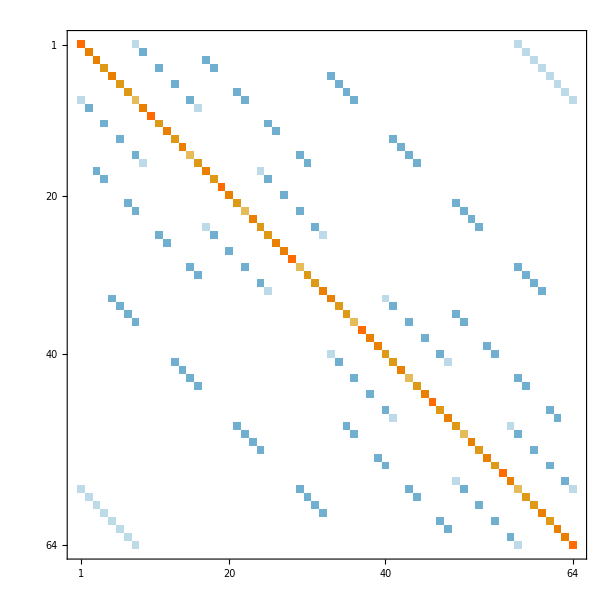

```mathematica
MatrixPlot[H]
```

```mathematica
Sort[Eigenvalues[H]]
```

{0.97904,4.96887,4.96887,4.96887,4.96887,4.96887,4.96887,5.,5.,5.,8.82186,8.93845,8.93845,8.93845,8.93845,8.93845,8.93845,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,9.,13.,13.,13.,13.,13.,13.,13.,13.,13.,13.,13.,13.,13.,13.,13.0311,13.0311,13.0311,13.0311,13.0311,13.0311,13.0616,13.0616,13.0616,13.0616,13.0616,13.0616,13.1991}

```mathematica
zeroH =SparseArray[
{{1,1}->13.000+0.000 I,{1,2}->-0.500+0.000 I,{1,9}->-0.500+0.000 I,{2,1}->-0.500+0.000 I,{2,2}->7.000+0.000 I,{2,3}->-2.000+0.000 I,{2,4}->-2.000+0.000 I,{2,6}->-2.000+0.000 I,{2,10}->-0.500+0.000 I,{3,2}->-2.000+0.000 I,{3,3}->7.000+0.000 I,{3,5}->-2.000+0.000 I,{3,7}->-2.000+0.000 I,{4,2}->-2.000+0.000 I,{4,4}->7.000+0.000 I,{4,5}->-2.000+0.000 I,{4,8}->-2.000+0.000 I,{5,3}->-2.000+0.000 I,{5,4}->-2.000+0.000 I,{5,5}->7.000+0.000 I,{5,9}->-2.000+0.000 I,{6,2}->-2.000+0.000 I,{6,6}->7.000+0.000 I,{6,7}->-2.000+0.000 I,{6,8}->-2.000+0.000 I,{7,3}->-2.000+0.000 I,{7,6}->-2.000+0.000 I,{7,7}->7.000+0.000 I,{7,9}->-2.000+0.000 I,{8,4}->-2.000+0.000 I,{8,6}->-2.000+0.000 I,{8,8}->7.000+0.000 I,{8,9}->-2.000+0.000 I,{9,1}->-0.500+0.000 I,{9,5}->-2.000+0.000 I,{9,7}->-2.000+0.000 I,{9,8}->-2.000+0.000 I,{9,9}->7.000+0.000 I,{9,10}->-0.500+0.000 I,{10,2}->-0.500+0.000 I,{10,9}->-0.500+0.000 I,{10,10}->13.000+0.000 I}]
```

SparseArray::posr: The left-hand side of {9,0}→-0.5+0. ⅈ in {{1,1}→13.+0. ⅈ,{1,2}→-0.5+0. ⅈ,{1,9}→-0.5+0. ⅈ,{2,1}→-0.5+0. ⅈ,{2,2}→7.+0. ⅈ,{2,3}→-2.+0. ⅈ,{2,4}→-2.+0. ⅈ,{2,6}→-2.+0. ⅈ,{2,10}→-0.5+0. ⅈ,{3,2}→-2.+0. ⅈ,«20»,{8,5}→-2.+0. ⅈ,{8,7}→7.+0. ⅈ,{8,8}→-2.+0. ⅈ,{9,0}→-0.5+0. ⅈ,{9,4}→-2.+0. ⅈ,{9,6}→-2.+0. ⅈ,{9,7}→-2.+0. ⅈ,{9,8}→7.+0. ⅈ,{9,9}→-0.5+0. ⅈ} is not a position or a pattern that will match the position of an element in an array with depth 2.

SparseArray[{{1,1}→13.+0. ⅈ,{1,2}→-0.5+0. ⅈ,{1,9}→-0.5+0. ⅈ,{2,1}→-0.5+0. ⅈ,{2,2}→7.+0. ⅈ,{2,3}→-2.+0. ⅈ,{2,4}→-2.+0. ⅈ,{2,6}→-2.+0. ⅈ,{2,10}→-0.5+0. ⅈ,{3,2}→-2.+0. ⅈ,{3,2}→7.+0. ⅈ,{3,4}→-2.+0. ⅈ,{3,6}→-2.+0. ⅈ,{4,1}→-2.+0. ⅈ,{4,3}→7.+0. ⅈ,{4,4}→-2.+0. ⅈ,{4,7}→-2.+0. ⅈ,{5,2}→-2.+0. ⅈ,{5,3}→-2.+0. ⅈ,{5,4}→7.+0. ⅈ,{5,8}→-2.+0. ⅈ,{6,1}→-2.+0. ⅈ,{6,5}→7.+0. ⅈ,{6,6}→-2.+0. ⅈ,{6,7}→-2.+0. ⅈ,{7,2}→-2.+0. ⅈ,{7,5}→-2.+0. ⅈ,{7,6}→7.+0. ⅈ,{7,8}→-2.+0. ⅈ,{8,3}→-2.+0. ⅈ,{8,5}→-2.+0. ⅈ,{8,7}→7.+0. ⅈ,{8,8}→-2.+0. ⅈ,{9,0}→-0.5+0. ⅈ,{9,4}→-2.+0. ⅈ,{9,6}→-2.+0. ⅈ,{9,7}→-2.+0. ⅈ,{9,8}→7.+0. ⅈ,{9,9}→-0.5+0. ⅈ}]